```mathematica
SetDirectory[NotebookDirectory[]];
Get["DSLib.wl"];
Get["APILib.wl"];
```

```mathematica
DSLib`BuildDatasetIndex["teste.txt", "BATEIAS", True];
```

```mathematica
DSLib`BuildDatasetIndex["index.txt", "BATEIAS", True];
DSLib`DatasetInfo["index.txt"];
ds = ReadList["index.txt"];
DSLib`NextIndex[ds, 1, 1, "Hour"];
DSLib`HourRegister[ds[[1;;5]]];
DSLib`BuildMonthDataset[ds,1];
DSLib`BuildDatasetHourly["index.txt",False];
DSLib`TailDataLog[2,"Hours"];
DSLib`HeadDataLog[2,"Hours"];
DSLib`SystemStatus["index.txt"];
```

102

<|file→DATASETS\2021-03,last→{91,99}|>

<|file→DATASETS\2021-03,last→{100,100}|>

102

<|file→DATASETS\2021-03,last→{100,100}|>

```mathematica
DSLib`RunCalibration[1,"Week",DSLib`calibration, {}, False];
DSLib`RunCalibration[1,"Week",DSLib`calibration, DSLib`TailDataLog[1,"Week"]];
Get["DATASETS/calibration.txt"]
```

```mathematica
Get["APILib.wl"];
APILib`PlotBushDataLog["B1381", 7*24, "Hours"]
APILib`PNGPlotBushDataLog[ 7*24, "Hours"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
Get["DSLib.wl"];
Get["APILib.wl"];
APILib`ShowLastMeasure["index.txt","1","138", "Period"->24]
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-BUSHING 138KV from Mon 14 Jun 2021 07:15:55 to Tue 15 Jun 2021 08:14:23DF = Dissipation Factor (%) and C = Capacitance (pF)

```mathematica
Options[APILib`ShowLastMeasure]
```

{Period→24,Unit→Hour}

```mathematica
APILib`ShowSystemStatus["index.txt"]
```

Local time is Tue 8 Jun 2021 15:37:12<H3> SYSTEM ALERT - ACTION IS REQUIRED</H3><P>CHECK THE SYSTEM HEALTH AT SUBSTATION<P>Last update received at: Tue 8 Jun 2021 12:10:31<P>Elapsed time from last update time: 3.44423 hours<P>Most recent data acquired from Tue 8 Jun 2021 10:59:03 to Tue 8 Jun 2021 11:04:38<P>Most recent file processed: 119.fasor<P>Historical data available from Fri 4 Jun 2021 12:13:19 to Tue 8 Jun 2021 11:04:38

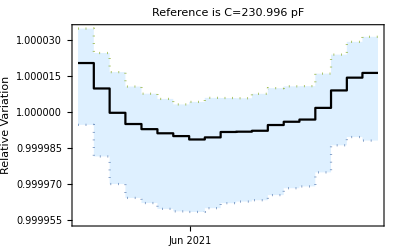

```mathematica
APILib`PlotCapTrend["CA1381",1,"Day","Hours"]
```

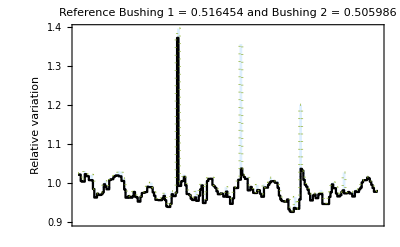

```mathematica
APILib`PlotDFTrend["FA1381",1,"Day","Hours"]
```

```mathematica
APILib`FAPIPlotDataLog
```

```mathematica
APILib`FAPIPlotCapTrend
```

```mathematica
APILib`FAPIPlotDFTrend
```

### Export Functions

```mathematica
CloudPublish[ FAPIPlotDatalog,"datalog"]
CloudPublish[ FAPIPlotDFTrend,"trenddf"]
CloudPublish[FAPIPlotCapTrend,"trendcap"]
(* REST API TO ADD A NEW CISEI FILE TO THE INDEX *)
CloudDeploy[APIUpdateDatasetIndex,"update"]
(* CHECK SYSTEM HEATH AND UPDATE HOURDATASET *)
CloudDeploy[ScheduledTask[ SystemStatus[],Quantity[2,"Hours"]],"systemcheck"]
```

```mathematica
CloudObject[["https://www.wolframcloud.com/obj/i.chueiri/datalog"](https://www.wolframcloud.com/obj/i.chueiri/datalog)]
CloudObject[["https://www.wolframcloud.com/obj/i.chueiri/trendcap"](https://www.wolframcloud.com/obj/i.chueiri/trendcap)]
CloudObject[["https://www.wolframcloud.com/obj/i.chueiri/trenddf"](https://www.wolframcloud.com/obj/i.chueiri/trenddf)]
```

<|file→DATASETS\2021-03,last→{2449,2449}|>

SYSTEM IS DOWN FOR MORE THAN 23.8205 hours.

Please, check the system health using RDP.

```mathematica
DSLib`BuildDatasetIndex["index.txt", "BATEIAS", True];
DSLib`BuildDatasetHourly["index.txt",False];
DSLib`RunCalibration[1,"Week",DSLib`calibration, {}, True];
```

2000

<|file→DATASETS\2021-03,last→{1990,1998}|>

<|file→DATASETS\2021-03,last→{1999,1999}|>

```mathematica
Reap[ Sow[1,"a"]; Sow[2,"a"]; Sow[-3,"b"],{"a", "b"},#1->Total[#2] &]
```

{-3,{{a→3},{b→-3}}}

```mathematica
Clear[teste];
Options[teste] = {"x"-> 33, "y"->4};
teste[a_,b_, OptionsPattern[]] :=  Return [a + b + OptionValue["x"] *OptionValue["y"]];
```

```mathematica
teste[1,2]
```

36

```mathematica
teste[1,2,"x"->3, "y"->5]
```

18

{A1,B1,A2,B2}

```mathematica
r=ReadList[ReadList["index.txt"][[-2,2]]];
```

```mathematica
APILib`KC
```

<|KV→<|AA138→17.9929,AA230→29.1554,AB138→17.9196,AB230→29.0356,AC138→17.9934,AC230→29.2245|>,KI→<|AIA2301→0.0000131955,AIA2302→0.0000135952,AIB2301→0.0000129049,AIB2302→0.0000125328,AIC2301→0.0000113279,AIC2302→0.0000136547,AIA1381→0.0000138666,AIA1382→0.0000134205,AIB1381→0.0000117557,AIB1382→0.0000138912,AIC1381→0.0000127748,AIC1382→0.0000139418|>|>

<|file→73.fasor,data→Sat 5 Jun 2021 09:00:44GMT-3,FA1381→0.248815,FA1382→0.395723,FB1381→0.271737,FB1382→0.211866,FC1381→0.339396,FC1382→0.291986,FA2301→0.403007,FA2302→0.38333,FB2301→0.324268,FB2302→0.367209,FC2301→0.283447,FC2302→0.361643,CA1381→229.684,CA1382→230.738,CB1381→240.169,CB1382→229.921,CC1381→239.641,CC1382→229.706,CA2301→286.658,CA2302→276.834,CB2301→282.66,CB2302→295.792,CC2301→289.844,CC2302→289.7|>

```mathematica
Get["APILib.wl"];
APILib`Calibrate[r[[1]]]
```

<|file→73.fasor,data→Sat 5 Jun 2021 09:00:44GMT-3,FA1381→0.248815,FA1382→0.395723,FB1381→0.271737,FB1382→0.211866,FC1381→0.339396,FC1382→0.291986,FA2301→0.403007,FA2302→0.38333,FB2301→0.324268,FB2302→0.367209,FC2301→0.283447,FC2302→0.361643,CA1381→229.684,CA1382→230.738,CB1381→240.169,CB1382→229.921,CC1381→239.641,CC1382→229.706,CA2301→286.658,CA2302→276.834,CB2301→282.66,CB2302→295.792,CC2301→289.844,CC2302→289.7|>

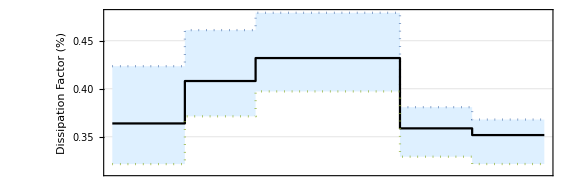
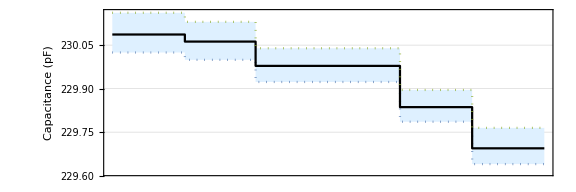
Calibration: Dissipation Factor=0.36 Capacitance=230 pF
-Graphics-
-Graphics-BUSH X1 TRANSFORMER ATF-C

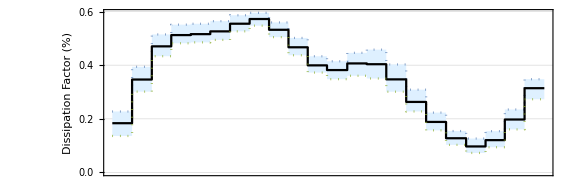
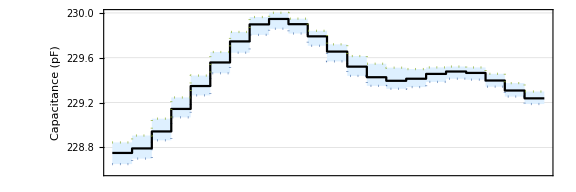
Calibration: Dissipation Factor=0.36 Capacitance=230pF
-Graphics-
-Graphics-BUSH X1 TRANSFORMER ATF-C

```mathematica
SetDirectory[NotebookDirectory[]];
Get["DSLib.wl"];
Get["APILib.wl"];
Options[APILib`PlotDataLog]={"MovingAverage"->4};
APILib`PlotBushDataLog["A1381",24,"Days"]
```